```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210603_bar_charts_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
subsetpositionsforsequences=Import["cases/subsetpositionsforsequences.mx"];
boundaries=Import["cases/boundaries_-5and5_105.mx"];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_]:=Module[{coefficients,objectivefunctions,solutionvectors},
coefficients=Table[RandomReal[{-10,-20},Length@subsetpositions],300];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,300}];
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{objectivefunctions,solutionvectors}]
```

```mathematica
AbsoluteTiming[resultset=Quiet@Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,i],{i,subsetpositionsforsequences}];]
```

{6445.66,Null}

```mathematica
Export["C:/Users/serha/NonDrive/OR_model-solution_vectors/-10-20solutionvectors_fxdbounds_-5and5_105pcs.mx",resultset[[All,2]]]
Export["C:/Users/serha/NonDrive/OR_model-objective_functions/-10-20objfunc_fxdbounds_-5and5_105pcs.mx",resultset[[All,1]]]
```

C:/Users/serha/NonDrive/OR_model-solution_vectors/-10-20solutionvectors_fxdbounds_-5and5_105pcs.mx

C:/Users/serha/NonDrive/OR_model-objective_functions/-10-20objfunc_fxdbounds_-5and5_105pcs.mx

```mathematica
solutionvectors=resultset[[All,2]];
objfunctions=resultset[[All,1]];(*Length@first[(Flatten[solutionvectors,1])ᵀ]
Length@(Flatten[solutionvectors,1])[[first@Flatten[solutionvectors,1],All]]*)
```

```mathematica
(*solutionvectors=Import["C:/Users/serha/NonDrive/OR_model-solution_vectors/-2-4solutionvectors_fxdbounds_-5and5_105pcs.mx"];*)
```

```mathematica
SeedRandom@25;
randomreactionlist=Table[Sort@RandomInteger[{1,fluxexchanges},i],{i,Range[1008,500,-50]}];
```

```mathematica
solutionvectorsreactionsdeleted=Table[Partition[Flatten[solutionvectors,1][[All,i]],300],{i,randomreactionlist}];
```

```mathematica
objfunctionsreactionsdeleted=Table[Partition[Flatten[objfunctions,1][[All,i]],300],{i,randomreactionlist}];
```

```mathematica
AbsoluteTiming[featuredatalist=Table[Table[MapThread[Dot,{objfunctionsreactionsdeleted[[j]][[i]],solutionvectorsreactionsdeleted[[j]][[i]]}],{i,200}],{j,10}];]
```

{50.1407,Null}

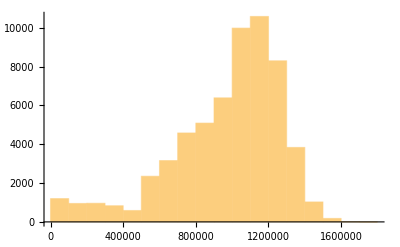
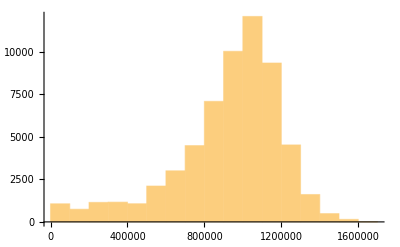
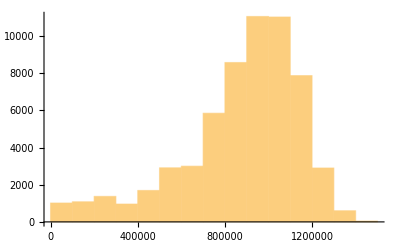
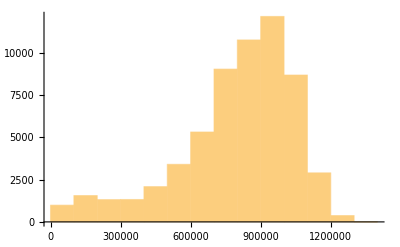
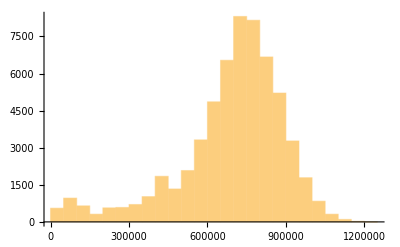
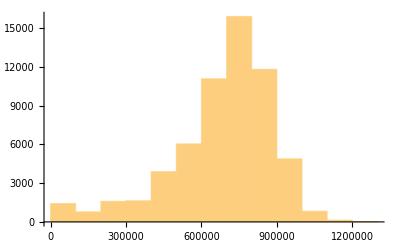
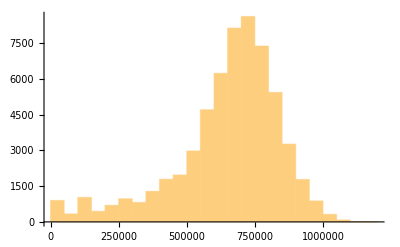
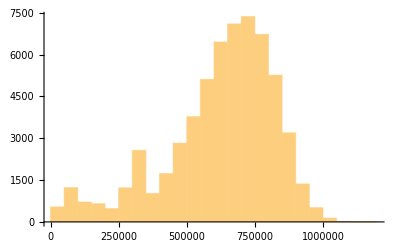

```mathematica
datafulllist=Table[Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[featuredatalist[[j]],1],1],2],{j,10}];
Table[Histogram@datafulllist[[i]][[All,3]],{i,10}]
```

```mathematica
thread=Thread[{Range@10,Range[32500,23250,-1000]}]
```

{{1,32500},{2,31500},{3,30500},{4,29500},{5,28500},{6,27500},{7,26500},{8,25500},{9,24500},{10,23500}}

```mathematica
AbsoluteTiming[widthdataFixedstep2=Table[snetworkdatabinned[3,i[[2]],datafulllist[[i[[1]]]]],{i,thread}];]
```

{63.7878,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataFixedstep2[[i]][[1]],widthdataFixedstep2[[i]][[2]],2,7,400,Green],{i,10}];
graphsandnodenumbers12[[All,2]]
```

{53,52,49,46,43,48,45,45,42,42}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{142.612,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{53,52,49,46,43,48,45,45,42,42}

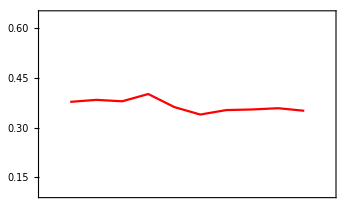
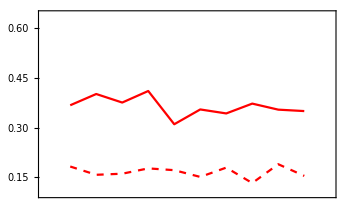
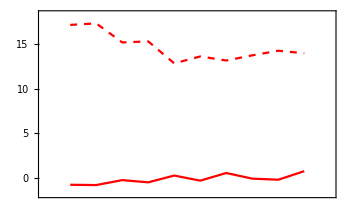

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=Table[snetworkdatafxdbucket[3,bucketnode12[[i]],datafulllist[[i]]],{i,10}];]
```

{22.9517,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataFixedbucket2[[i]][[1]],widthdataFixedbucket2[[i]][[2]],1.5,7,400,Green],{i,10}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{239.613,Null}

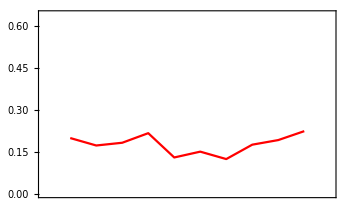
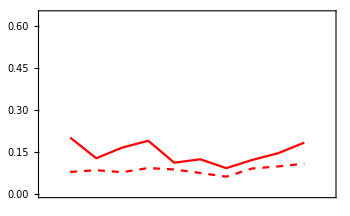
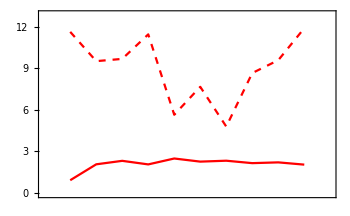

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_bounds/(-10,-20)-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_bounds/(-10,-20)-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_bounds/(-10,-20)-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_bounds/(-10,-20)-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_bounds/(-10,-20)-modularityvalues-fss.mx

plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_bounds/(-10,-20)-zscores-fss.mx

plot_values/fxd_bounds/(-10,-20)-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-10,-20)-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-10,-20)-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-10,-20)-zscores-fbs.mx